-Graphics-

# Wolfram Language

## Computação para Ciências dos Dados

PÓS-GRADUAÇÃO EM DATA SCIENCE E DECISÃO

Prof. Daniel Carvalho @danielscarvalho

## Dica do Dia: 010

Este é o ambiente notebook (UI) da Wolfram, criado em 1988 no Mathematica 1.0 para realização de computação científica exploratória, versão atual 12.1. 

Use a combinação das teclas Shift + Enter para processar a célula de input.

Treinamento básico:

```mathematica
u=10/2+1/9-4
```

10/9

```mathematica
N[u,20]
```

1.1111111111111111111

O kernel do sistema é simbólico, a maioria das linguagens de programação são numéricas.
Note abaixo que o valor de x não foi definido, mas o sistema é capaz de processar!

```mathematica
1/(2x) *1/ Sqrt[x]
```

1/(2 x^(3/2))

A Wolfram Language trabalha com precisão arbitrária não depende do tamanho da palavra do SO (32, 64 bits...) ou capacidade da variável numérica.

```mathematica
N[π,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

Vamos ver algumas funções:

```mathematica
Plus[10,3]
```

13

```mathematica
Plus[x,5]
```

5+x

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[x,{x,-10,10}]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Solve[x^2+3x+2==0,x]
```

{{x→-2},{x→-1}}

```mathematica
Table[Solve[x^2+3x+2==z,x],{z,0,10}]
```

{{{x→-2},{x→-1}},{{x→1/2 (-3-√5)},{x→1/2 (-3+√5)}},{{x→-3},{x→0}},{{x→1/2 (-3-√13)},{x→1/2 (-3+√13)}},{{x→1/2 (-3-√17)},{x→1/2 (-3+√17)}},{{x→1/2 (-3-√21)},{x→1/2 (-3+√21)}},{{x→-4},{x→1}},{{x→1/2 (-3-√29)},{x→1/2 (-3+√29)}},{{x→1/2 (-3-√33)},{x→1/2 (-3+√33)}},{{x→1/2 (-3-√37)},{x→1/2 (-3+√37)}},{{x→1/2 (-3-√41)},{x→1/2 (-3+√41)}}}

```mathematica
ListPlot3D[Table[Sinc[x]*Sinc[y],{x,-10,10,.1},{y,-10,10,.1}],ColorFunction->Hue,PlotRange-> All]
```

-Graphics3D-

É a plataforma mais poderosa para resolver cálculos, recentente todos os problemas dos principais livros acadêmicos de cálculos foram testados com sucesso:

```mathematica
Integrate[x^2+3x+Cos[x],x] //TraditionalForm
```

(3 x^2)/2+x x.b2+sin(x)

```mathematica
D[x^2+3x+Cos[x],x] //TraditionalForm
```

3-sin(x)

Em uma linha de comando podemos criar uma interface:

```mathematica
Manipulate[Plot[Sin[a fx]*Cos[a fy],{a,-10,10}],
{fx,1,10},
{fy,1,10}]
```

Como realizar uma transformada de fourier? Use a função Fourier, simples assim, a função tem o nome relacionado!
Pressione F1 para o help

```mathematica
?Four*
```

```mathematica
?Fourier
```

```mathematica
Manipulate[
ListLinePlot[view@Fourier[Table[Sin[a fx]*Cos[a fy],{a,-10,10}]],PlotRange-> All],
{fx,1,10},
{fy,1,10},
{view,{Im,Re}}]
```

Pronto, treinamento acabou, agora vamos lá:

É possível realizar computação avançada neste ambiente, vamos iniciar com NLP, a plataforma tem dados acurados e computáveis. 
Diversos sistemas populares utilizam estes recursos da Wolfram, mas você nem imagina!! :-)

Pressionando = no início de uma nova célula para realizar consultas em inglês, em linguagem natural (Shift + Enter para processar)

What is Sonia Braga age?

69 9

How many days the Brazil president is in charge?

Jair Bolsonaro  (from January 1, 2019  to  present)

Distance from NYC to Paris

3618.85 mi

Distance from Diadema to Registro in kilometers

153.273 km

WolframAlphaQueryParseResults

21 °C

What is the boiling point of water?

99.9839 °C

WolframAlphaQueryResults

70.41 °C

WolframAlphaQueryParseResults

{Day: Fri 3 Apr 2020,241.41 $}

WolframAlphaQueryParseResults

381100 people

WolframAlphaQueryParseResults

4.68293×10^7 people

WolframAlphaQueryParseResults

6.92932×10^6 people

```mathematica
TextStructure["What is the boiling point of water at the mount Everest?"]
```

What
Wh-Pronoun
Wh-Noun Phraseis
Verb    the
Determinerboiling
Adjectivepoint
Noun
Noun Phrase  of
Preposition    water
Noun
Noun Phrase  at
Preposition  the
Determinermount
Proper NounEverest
Proper Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Noun Phrase?
Punctuation
Clause

Como está o céu agora, onde estou?

WolframAlphaQueryResults

-Graphics-SENW

```mathematica
GeoGraphics[GeoDisk[Entity["City",{"SaoPaulo","SaoPaulo","Brazil"}],Quantity[1, "Kilometers"]]]
```

-Graphics-

```mathematica
Here
```

GeoPosition[{-23.63,-46.63}]

WolframAlphaQueryParseResults

GeoPosition[{-23.63,-46.63}]

Há dados computáveis anatômicos, de química, humano, cachorro, gato, cavalo, genoma, medicamentos, doenças etc...

```mathematica
AnatomyPlot3D[Entity["AnatomicalStructure","PrefrontalCortex"],"PlotTheme"->"Scientific"]
```

-Graphics3D-

```mathematica
ProteinData["A2M","MoleculePlot"]
```

-Graphics3D-

WolframAlphaQueryParseResults

-Graphics3D-

WolframAlphaQueryParseResults

-Graphics-

WolframAlphaQueryParseResults

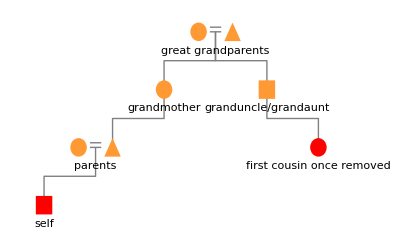

Faça um pedido bem definido e o sistema transforma em código:

WolframAlphaQueryParseResults

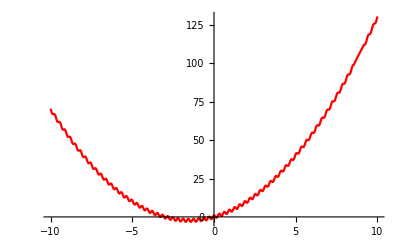

Há dados acurados computáveis como parte da plataforma, isso aliado a capacidade de processamento simbólico, e programação funcional, torna o ambiente ideal para realizar IA e ML:

```mathematica
FacialFeatures[-Graphics-] //Dataset
```

```mathematica
ImageIdentify[-Graphics-]
```

terrier

Quanto mais tempo a WL tem para trabalhar, melhor a resposta:

```mathematica
Table[ImageIdentify[-Graphics-,SpecificityGoal->g],{g,0,1,.1}]
```

{animal,terrier,terrier,terrier,terrier,terrier,terrier,terrier,terrier,terrier,Yorkshire terrier}

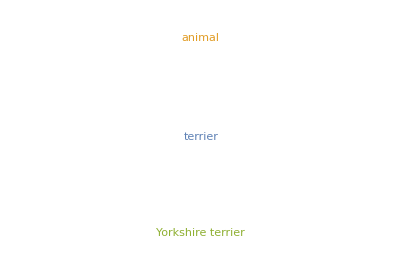

```mathematica
WordCloud[%]
```

```mathematica
i=-Graphics-;
```

```mathematica
ImageBoundingBoxes[i]
```

<|domestic cat→{Rectangle[{50.0503,48.6728},{381.29,504.017}]}|>

```mathematica
HighlightImage[i,%]
```

-Graphics-

Ops! Cade a maça! Ver o help da função ImageBoundingBoxes...

Vamos buscar imagens na Inernet para treinamento:

```mathematica
dog =WebImageSearch["dog","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cat =WebImageSearch["cat","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
trex =WebImageSearch["t-rex","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Vamos observar as imagens em forma de cluster, note que as imagens são organizadas na arvore não o conteúdo (animais)...
Há diversas funções para realizar classificação, regressão, clusterização entre outros algoritmos que estão na moda.

```mathematica
ClusteringTree[Flatten[{cat,dog,trex}]]
```

-Graphics-

Agora vamos criar e treinar um classificador, em uma linha de comando:

```mathematica
animal= Classify[<| 
"cão" -> dog,
"gato" -> cat,
"t-rex" -> trex
|>]
```

ClassifierFunction[…]

Teste com imagem de um lagarto...

```mathematica
animal[-Graphics-]
```

t-rex

O que está pegando no NYT hoje?

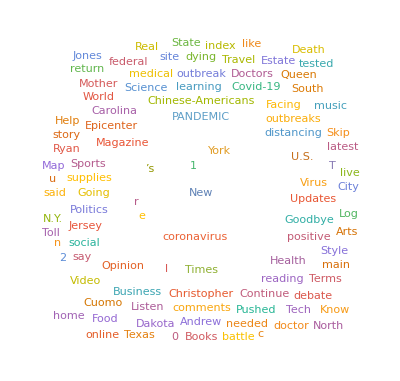

```mathematica
WordCloud[DeleteStopwords[Import["http://www.nyt.com"]]]
```

Função em Wolfram Language que implementei e foi publicada:

```mathematica
ResourceFunction["SequenceGraph"]
```

{1,2,3,4,5,6,7,8,9,10}

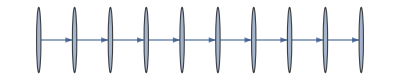

```mathematica
Range[10]
[%]
```

```mathematica
RandomInteger[10,100]
[%]
```

{2,3,6,9,1,6,0,2,2,10,6,4,7,6,2,4,3,10,0,7,0,5,2,0,3,8,7,10,5,5,9,8,0,3,2,7,0,1,4,6,2,9,7,0,3,4,5,6,10,9,7,4,7,4,8,1,4,2,8,5,6,3,2,8,8,5,5,8,3,1,3,3,5,5,0,8,8,0,1,3,8,9,4,3,1,10,10,10,10,6,4,7,8,5,9,10,7,8,9,9}

-Graphics-

Agora vamos gerar um grafo do livro “Alice no pais das maravilhas”, em uma única linha de código, cada nó é uma palavra na ordem que aparece no livro.

```mathematica
ResourceFunction["SequenceGraph"][StringSplit[DeleteStopwords[ResourceData["Alice in Wonderland"]],RegularExpression["\\W+"]]]
```

-Graphics-

Usando outra função que publiquei que consome a API do DuckDuckGo:

```mathematica
ResourceFunction["DuckDuckGoQuery"]
```

```mathematica
["Alan Turing"]["Image"]
```

https://duckduckgo.com/i/a377e75e.jpg

```mathematica
atImage=Import[%]
```

-Graphics-

```mathematica
Classify["NotablePerson",atImage]
```

Alan Turing

Alan Turing é uma Entity com semântica, ou seja, o sistema sabe o que é “Alan Turing” assim como “Brazil”, “São Paulo”, “Moon”, etc...:

```mathematica
Entity["Person","AlanTuring::2f4s8"]["Dataset"]
```

```mathematica
FindFaces[atImage,"Image"]
```

{-Graphics-}

Processamento de imagens:

```mathematica
ColorNegate[EdgeDetect[Blur[atImage,5],5]]
```

-Graphics-

```mathematica
ImageIdentify[atImage]
```

person

Entity, um elemento que tem semântica... Ctrl = para definir uma entity...

```mathematica
Entity["Country","Brazil"]
```

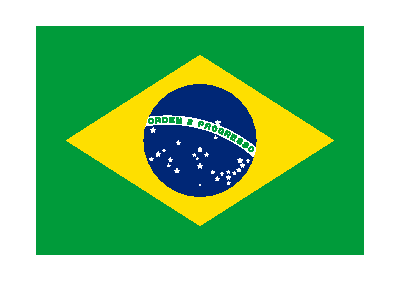

```mathematica
Entity["Country","Brazil"]["Flag"]
```

```mathematica
Entity["Country","Brazil"]["GDP"]
```

1.86863×10^12 $

```mathematica
Entity["Country","China"][]/Entity["Country","Brazil"][]
```

7.28244

```mathematica
Entity["Country","UnitedStates"][EntityProperty["Country","Dependencies"]]
```

{American Samoa,Guam,Northern Mariana Islands,Puerto Rico,United States Minor Outlying Islands,United States Virgin Islands}

```mathematica
Entity["Country","Brazil"][EntityProperty["Country","Dependencies"]]
```

{}

É possível definir “entities” junto a banco de dados da instituição. Desta forma as colunas do seu banco de dados relacional passam a ter propriedades semânticas e se integram ao contexto da Wolfram Language.

Para finalizar por hoje:

WolframAlphaQueryResults

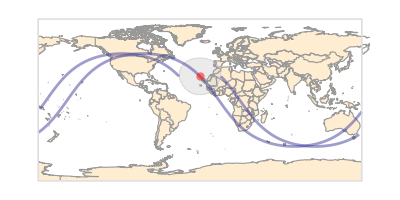

WolframAlphaQueryResults

42
(according to the book The Hitchhiker's Guide to the Galaxy, by Douglas Adams)

Podemos obter dados de BITCOINs via WEB API no formato JSON e carregar em um dataset (Data Frame):

```mathematica
btc=Dataset[Import["https://www.mercadobitcoin.net/api/BTC/trades/","RawJSON"]]
```

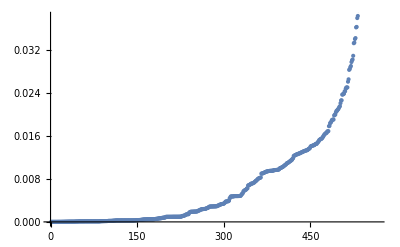

```mathematica
ListPlot[Sort[btc[Select[#type=="buy"&],"amount"]],ColorFunction->"Rainbow"]
```

Agora vamos publicar este notebook na nuvem, gerar um short URL e um QRCode para acesso fácil:

```mathematica
CloudPublish[]
```

Ou no client (Mathematica) File, Publish to Cloud...

```mathematica
URLShorten["www.wolframcloud.com/obj/dcarvalho/Published/Insper-Dica-010.nb"]
```

https://wolfr.am/LBbZEwAP

```mathematica
BarcodeImage[ "https://wolfr.am/LBbZEwAP","QR"]
```

-Graphics-

Vou também exportar como PDF...

Notou que não foram importadas bibliotecas externas...

## Para saber mais:

www.wolfram.com

www.wolframalpha.com

https://www.wolfram.com/language/fast-introduction-for-programmers/en/

https://www.wolfram.com/language/elementary-introduction/2nd-ed/

https://www.wolfram.com/wolfram-u/